# Compare Julia to MM

Original code for micromagnetic computation was provided in Mathematica. The algorithms were then written in Julia and are checked against the original Mathematica code here. In Sections 1 and 2 you can change parameters and redo calculations by running the script. Results are imported and presented in the rest of the notebook. 

Note: Mathematica code does not implement PBC . This means that when pbc=True, results between both methods will not agree.

## 0. Parameters

```mathematica
(* Values here must match the ones in "save-all-julia-data.jl" *)
Nx=Ny=128;
H=-0.02;
ED= 0.001*0;
β=1;
Dz=N[4π β ED];
DDM=0.1;
J=1.0;
T = 0.0;
damping = 0.01;
pbc=1.0;(**)
dx=Nx/2;
dir=ParentDirectory[NotebookDirectory[]]<>"/02-data/test/";

Extrap0={0.,0.,0.};     (* Free boundary conditions *)
Extrap1={2.,-1.,0.};    (* First-order extrapolated boundary conditions *)
Extrap2={3.,-3.,1.};    (* Second-order extrapolated boundary conditions *)
Extrap=Extrap1;
E1=Extrap[[1]];    E2=Extrap[[2]];    E3=Extrap[[3]];
```

## 1. Run julia script

```mathematica
(* This works on Linux and Mac. I do not think it works in windows 
because "./" does not execute a script there. Need to run the file
"save-all-julia-data.jl" to save
 *)
SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/01-scripts/"];
RunProcess[{"TEST.jl",H,DDM,Dz,ED,T,damping,pbc, Nx}]
```

<|ExitCode→0,StandardOutput→Saving results in /home/amel/Documents/skyrmion-micromagnetics/julia-files-edit/02-data/test/

Saving energy
,StandardError→|>

## 2. Run Mathematica definitions

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[{MatrixPlot,ListVectorPlot},ImageSize->400,ImagePadding->{{50,70},{50,50}},LabelStyle->{Directive["Times",14,Black],FontFamily->"Times"}];
SetOptions[{ListPlot,ListLogPlot,ListLogLogPlot,Plot,LogPlot,LogLogPlot,Histogram},Frame->True,AspectRatio->1/GoldenRatio,ImageSize->600,LabelStyle->{Directive["Times",18,Black],FontFamily->"Times",ImagePadding->{{100,100},{100,100}}}];
```

```mathematica
Test=True;
     Nz=10;  (* Particle's dimensions. *)
NSites=NSpins=Nx Ny;
      (* The number of sites (spins) *)
α=1;   (* Damping *)
J=1;      (* Exchange constant *)

β=1;   (* β=4π ED / Dz *)

(*δW=√(J/Dz);  (* Domain wall width *)
*)
(* Relaxation control *)
NRot=4;
Tol=10^-5 NRot; (* Tolerance for stopping relaxation: 10^-6 NRot *)
kMax=10^5;

(* Evaluation control *)
hStep=0.2; 
t0=0;     
tMax=1. 10^6;   (* Initially defined time of the evolution *)
Samp=1;   (* Rarification coefficient for sampling *)
NSampPlaquette=50;   (* Sampling points per plaquette *)
NtPointsPlaquette=NSampPlaquette Samp;   (* RK4 steps per plaquette *)
tPlaquette=hStep NtPointsPlaquette;  (* Evolution time for one plaquette *)
NPlaquettes=Round[(tMax-t0)/tPlaquette];   (* Number of plaquettes *)
tMax=tPlaquette NPlaquettes+t0;   (* Redefined tMax *)
NSampPoints=NSampPlaquette NPlaquettes;  (* Total number of sampled points *)
tFree = tPlaquette;
tMax=2. 10^4;
```

```mathematica
Energy=With[{Nx=Nx,Ny=Ny,J=J,Dz=Dz,FHD=FHD,pbc=pbc==1.0},Compile[{{s,_Real,3},H,ED},Module[{HD},
HD= ED FHD[s];
-J∑_(α=1)^3 ∑_(nx=1)^Nx ∑_(ny=1)^Ny s[[α,nx,ny]]  (If[nx>1,s[[α,nx-1,ny]],If[pbc,s[[α,Nx,ny]],0.]] + If[ny>1, s[[α,nx,ny-1]],If[pbc,s[[α,nx,Ny]],0.]] )+If[pbc,2J Nx Ny,J(2Nx Ny-Nx-Ny)]-0.5Dz ∑_(nx=1)^Nx ∑_(ny=1)^Ny (s[[3,nx,ny]]^2-1)-H ∑_(nx=1)^Nx ∑_(ny=1)^Ny s[[3,nx,ny]]-∑_(α=1)^3 ∑_(nx=1)^Nx ∑_(ny=1)^Ny s[[α,nx,ny]]  (0.5HD[[α,nx,ny]])-DDM Sum[(If[nx>1,s[[2,nx,ny]] s[[3,nx-1,ny]]-s[[3,nx,ny]] s[[2,nx-1,ny]],If[pbc,s[[2,nx,ny]] s[[3,Nx,ny]]-s[[3,nx,ny]] s[[2,Nx,ny]],0.]] + If[ny>1, s[[3,nx,ny]]s[[1,nx,ny-1]]- s[[1,nx,ny]]s[[3,nx,ny-1]],If[pbc,s[[3,nx,ny]]s[[1,nx,Ny]]- s[[1,nx,ny]]s[[3,nx,Ny]],0.]] ),{nx,1,Nx},{ny,1,Ny}]
],CompilationTarget->"C",CompilationOptions->{"InlineCompiledFunctions"->True},"RuntimeOptions"->{"EvaluateSymbolically" -> False}]];
```

```mathematica
(* Dipolar field *)

ϕxx=With[{Nz=Nz},Compile[{{nx,_Integer},{ny,_Integer}},Which[nx==ny==0,0,True,(2. nx^2-ny^2)/((nx^2+ny^2)^(5/2))]+2/Nz Sum[(Nz-nz)(2. nx^2-ny^2-nz^2)/((nx^2+ny^2+nz^2)^(5/2)),{nz,1,Nz-1}],CompilationTarget->"C","RuntimeOptions"->"Speed"]];
ϕyy=With[{Nz=Nz},Compile[{{nx,_Integer},{ny,_Integer}},Which[nx==ny==0,0,True,(2. ny^2-nx^2)/((nx^2+ny^2)^(5/2))]+2/Nz Sum[(Nz-nz)(2. ny^2-nx^2-nz^2)/((nx^2+ny^2+nz^2)^(5/2)),{nz,1,Nz-1}],CompilationTarget->"C","RuntimeOptions"->"Speed"]];
ϕzz=With[{Nz=Nz},Compile[{{nx,_Integer},{ny,_Integer}},Which[nx==ny==0,0,True,-1/((nx^2+ny^2)^(3/2))]+2/Nz Sum[(Nz-nz)(2. nz^2-nx^2-ny^2)/((nx^2+ny^2+nz^2)^(5/2)),{nz,1,Nz-1}],CompilationTarget->"C","RuntimeOptions"->"Speed"]];
ϕxy=With[{Nz=Nz},Compile[{{nx,_Integer},{ny,_Integer}},Which[nx==ny==0,0,True,(3.nx ny)/((nx^2+ny^2)^(5/2))]+2/Nz Sum[(Nz-nz)(3.nx ny)/((nx^2+ny^2+nz^2)^(5/2)),{nz,1,Nz-1}],CompilationTarget->"C","RuntimeOptions"->"Speed"]];

Parallelize[
VDxx=Table[ϕxx[nx,ny],{nx,-Nx+1,Nx-1},{ny,-Ny+1,Ny-1}];
VDyy=Table[ϕyy[nx,ny],{nx,-Nx+1,Nx-1},{ny,-Ny+1,Ny-1}];
VDxy=Table[ϕxy[nx,ny],{nx,-Nx+1,Nx-1},{ny,-Ny+1,Ny-1}];
VDzz=Table[ϕzz[nx,ny],{nx,-Nx+1,Nx-1},{ny,-Ny+1,Ny-1}];
]; 

FHD[s_List]:={
ListConvolve[s[[1]],VDxx]+
ListConvolve[s[[2]],VDxy],ListConvolve[s[[2]],VDyy]+
ListConvolve[s[[1]],VDxy],ListConvolve[s[[3]],VDzz]};



(* Defining effective field for energy minimization. Transposed spin. I used this function to check that the free boundary conditions were working correctly *)
HEff2=With[{J=J,Nx=Nx,Ny=Ny,DMIBloch=True,DMINeel=False,Anis=False,AnisR=False,E1=E1,E2=E2,E3=E3,pbc=False,DMIpbc=False},Compile[{{s,_Real,3},H,DDM,Dz,{nx,_Integer},{ny,_Integer}},
Module[{HHEff,abr},

HHEff={0.0,0.0,H};

HHEff+=Table[
If[nx>1,J s[[nx-1,ny,α]],E1 s[[1,ny,α]]+ E2 s[[2,ny,α]]+E3 s[[3,ny,α]]]
+If[nx<Nx,J s[[nx+1,ny,α]],E1 s[[Nx,ny,α]]+E2 s[[Nx-1,ny,α]]+E3 s[[Nx-2,ny,α]]]
+If[ny>1,J s[[nx,ny-1,α]],E1 s[[nx,1,α]]+E2 s[[nx,2,α]]+E3 s[[nx,3,α]]]
+If[ny<Ny,J s[[nx,ny+1,α]],E1 s[[nx,Ny,α]]+E2 s[[nx,Ny-1,α]]+E3 s[[nx,Ny-2,α]]]
,{α,1,3}];

If[Anis,HHEff+={0.,0.,Dz s[[nx,ny,3]]}];

If[DMIBloch,
HHEff+={If[ny>1,-DDM s[[nx,ny-1,3]],If[DMIpbc,-DDM s[[nx,Ny,3]],0.]]+If[ny<Ny,DDM s[[nx,ny+1,3]],If[DMIpbc,DDM s[[nx,1,3]],0.]],
If[nx>1,DDM s[[nx-1,ny,3]],If[DMIpbc,DDM s[[Nx,ny,3]],0.]]+If[nx<Nx,-DDM s[[nx+1,ny,3]] ,If[DMIpbc,-DDM s[[1,ny,3]],0.]],
If[nx>1,-DDM s[[nx-1,ny,2]],If[DMIpbc,-DDM s[[Nx,ny,2]],0.]]+If[nx<Nx,DDM s[[nx+1,ny,2]],If[DMIpbc,DDM s[[1,ny,2]],0.]]+If[ny>1,DDM s[[nx,ny-1,1]],If[DMIpbc,DDM s[[nx,Ny,1]],0.]]+If[ny<Ny,-DDM s[[nx,ny+1,1]],If[DMIpbc,-DDM s[[nx,1,1]],0.]]}
];
HHEff
]]];

(* Defining effective field with DMI for Bloch skyrmions *)
HEff=With[{J=J,Nx=Nx,Ny=Ny,pbc=pbc,DDM=DDM,Dz=Dz,FHD=FHD,E1=E1,E2=E2,E3=E3},Compile[{{s,_Real,3},H,ED},
Module[{ans},

ans = Table[If[α==3,H,0.]+If[α==3,Dz s[[α,nx,ny]],0.]+J (
If[nx>1,s[[α,nx-1,ny]],E1 s[[α,1,ny]]+E2 s[[α,2,ny]]+E3 s[[α,3,ny]]]+
If[ny>1,s[[α,nx,ny-1]],E1 s[[α,nx,1]]+E2 s[[α,nx,2]]+E3 s[[α,nx,3]]]+
If[nx<Nx, s[[α,nx+1,ny]],E1 s[[α,Nx,ny]]+E2 s[[α,Nx-1,ny]]+E3 s[[α,Nx-2,ny]]]+
If[ny<Ny, s[[α,nx,ny+1]],E1 s[[α,nx,Ny]]+E2 s[[α,nx,Ny-1]]+E3 s[[α,nx,Ny-2]]]),{α,1,3},{nx,1,Nx},{ny,1,Ny}];

If[ED≠0.0,
ans += ED FHD[s],
ans 
];

If[DDM ≠0.0,ans+={Table[If[ny>1,-DDM s[[3,nx,ny-1]],0.0]+If[ny<Ny,+DDM s[[3,nx,ny+1]],0.0],{nx,1,Nx},{ny,1,Ny}], Table[If[nx>1,+DDM s[[3,nx-1,ny]],0.0]+If[nx<Nx,-DDM s[[3,nx+1,ny]],0.0],{nx,1,Nx},{ny,1,Ny}],Table[If[nx>1,-DDM s[[2,nx-1,ny]],0.0]+If[nx<Nx,+DDM s[[2,nx+1,ny]],0.0]+If[ny>1,+DDM s[[1,nx,ny-1]],0.0]+If[ny<Ny,-DDM s[[1,nx,ny+1]],0.0],{nx,1,Nx},{ny,1,Ny}]}, 

ans
]]]];
RHS=With[{HEff=HEff,α=0.01},Compile[{t,{s,_Real,3},{param,_Real,1}},Module[{h,sdotH,H,ED},
H=param[[1]];  ED=param[[2]];
h=HEff[s,H,ED]; sdotH=Sum[s[[i]]h[[i]],{i,1,3}];
{s[[2]]h[[3]]-s[[3]]h[[2]]+α(h[[1]]-s[[1]]sdotH),
s[[3]]h[[1]]-s[[1]]h[[3]]+α(h[[2]]-s[[2]]sdotH),
s[[1]]h[[2]]-s[[2]]h[[1]]+α(h[[3]]-s[[3]]sdotH)}
]]];

(* Defining RK4 and RK5 solvers *)
ClearAll[makeCompRK4]
makeCompRK4[f_]:=Compile[{{x0,_Real,3},{t0,_Real},{tMax,_Real},{n,_Integer},{samp,_Integer},{param,_Real,1}},Module[{h,K1,K2,K3,K4,SolList,x=x0,t,ksamp,nsamp},h=(tMax-t0)/n;nsamp=IntegerPart[n/samp];    
SolList=Table[x0,{nsamp+1}];

Do[t=t0+kh;ksamp=k/samp;
K1=hf[t,x,param];
K2=hf[t+(1/2)h,x+(1/2)K1,param];
K3=hf[t+(1/2)h,x+(1/2)K2,param];
K4=hf[t+h,x+K3,param];
x=x+(1/6)K1+(1/3)K2+(1/3)K3+(1/6)K4;If[FractionalPart[ksamp]==0,SolList[[IntegerPart[ksamp]+1]]=x];
,{k,1,n}];
SolList],CompilationOptions->{"InlineCompiledFunctions"->True},"RuntimeOptions"->"Speed"];

(* Creating compiled RK routine *)
RK=makeCompRK4[RHS];  (* RK5 has a poor stability here! Why?? *)

NormalizeSpins=With[{Nx=Nx,Ny=Ny},Compile[{{s,_Real,3}},Module[{S1,ss},
S1=s;
Do[
ss=s[[All,nx,ny]];
ss=ss/Norm[ss];
Do[S1[[α,nx,ny]]=ss[[α]],{α,1,3}];
,{nx,1,Nx},{ny,1,Ny}];
S1
]]];


SkyrmionQShape=Compile[{x,y,λ,Q,ϕ},Module[{r2,sz,sperp,ang},
r2=x^2+y^2;      sz=-(r2-λ^2)/(r2+λ^2);    sperp=√(1-sz^2);
ang=If[y>0,ArcCos[x/(√r2)],2π-ArcCos[x/(√r2)]];
{sperp Cos[Q ang+ϕ],sperp Sin[Q ang+ϕ],sz}]];

FSkyrmionQ=With[{Nx=Nx,Ny=Ny,SkyrmionQShape=SkyrmionQShape},Compile[{λ,Q,ϕ},
Table[SkyrmionQShape[nx-(Nx+1)/2,ny-(Ny+1)/2,λ,Q,ϕ][[α]],{α,1,3},{nx,1,Nx},{ny,1,Ny}]
]];
SkyrmionShape=Compile[{x,y,λ,a,Q,ϕ},{(2. ((x+a)Cos[ϕ]+y Sin[ϕ]) λ)/((x+a)^2+y^2+λ^2),Q(2.(y Cos[ϕ]-(x+a)Sin[ϕ]) λ)/((x+a)^2+y^2+λ^2),-(x^2+y^2-λ^2)/(x^2+y^2+λ^2)}];

FSkyrmion=With[{Nx=Nx,Ny=Ny,SkyrmionShape=SkyrmionShape},Compile[{λ,Q,ϕ},
Table[SkyrmionShape[nx-(Nx+1)/2,ny-(Ny+1)/2,λ,0.,Q,ϕ][[α]],{α,1,3},{nx,1,Nx},{ny,1,Ny}]
]];

FBiskyrmion=With[{Nx=Nx,Ny=Ny,SkyrmionShape=SkyrmionShape,NormalizeSpins=NormalizeSpins},Compile[{λ,a,Q1,Q2,ϕ1,ϕ2},
NormalizeSpins[Table[(SkyrmionShape[nx-(Nx+1)/2,ny-(Ny+1)/2,λ,a,Q1,ϕ1]+SkyrmionShape[nx-(Nx+1)/2,ny-(Ny+1)/2,λ,-a,Q2,ϕ2]+{0,0,1})[[α]],{α,1,3},{nx,1,Nx},{ny,1,Ny}]]
]];

FQ[s_]:=Module[{dxsQ,dysQ},
dxsQ=(-RotateRight[s,{0,2,0}]+8RotateRight[s,{0,1,0}]-8RotateRight[s,{0,-1,0}]+RotateRight[s,{0,-2,0}])/12;
dysQ=(-RotateRight[s,{0,0,2}]+8RotateRight[s,{0,0,1}]-8RotateRight[s,{0,0,-1}]+RotateRight[s,{0,0,-2}])/12;
1./(4π)Total[∑_(α=1)^3 ∑_(β=1)^3 ∑_(γ=1)^3 Signature[{α,β,γ}]s[[α]]dxsQ[[β]]dysQ[[γ]],∞]
];

(* Distance between the two skyrmions, if they are in different halves *)
Fd[s_]:=Module[{sl,sr,PosMaxl,PosMaxr},
sl=s[[3,1;;IntegerPart[(Nx+1)/2]]]; sr=s[[3,IntegerPart[(Nx+1)/2];;Nx]];
PosMaxl=Position[sl,Max[sl]][[1]];  PosMaxr=Position[sr,Max[sr]][[1]]+IntegerPart[(Nx+1)/2];
PosMaxr[[1]]-PosMaxl[[1]]-1
] 

GaussianSpins=With[{Nx=Nx,Ny=Ny},Compile[{},
Module[{},
Table[√(-2Log[RandomReal[]])Cos[2 π RandomReal[]],{α,1,3},{nx,1,Nx},{ny,1,Ny}]
],RuntimeAttributes->{Listable},Parallelization->True,CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False},"RuntimeOptions"->"Speed"]];

StripeDomainSpins=With[{Nx=Nx,Ny=Ny},Compile[{δ,d,{rot,_Integer}},
Module[{a},
Table[a=Tanh[d/(2δ)(2FractionalPart[nx/d]-1)(-1)^IntegerPart[nx/(d)]];Which[α==1,0,α==2,If[rot==1,Sign[Sin[(π nx)/d]],1] √(1-a^2),True,a],{α,1,3},{nx,1,Nx},{ny,1,Ny}]
],RuntimeAttributes->{Listable},Parallelization->True,CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False},"RuntimeOptions"->"Speed"]];

StripeDomainSpinsBlochWalls=With[{Nx=Nx,Ny=Ny},Compile[{δ,d,altsx,altsy,rotBL},
Module[{a},
Table[a=Tanh[d/(2δ)(2FractionalPart[nx/d]-1)(-1)^IntegerPart[nx/(d)]];Which[α==1,If[altsx==1,Sign[Sin[(π nx)/d]],1]Sin[rotBL(π (ny-1))/Ny] √(1-a^2),α==2,If[altsy==1,Sign[Sin[(π nx)/d]],1]Cos[rotBL(π (ny-1))/Ny] √(1-a^2),True,a],{α,1,3},{nx,1,Nx},{ny,1,Ny}]
],RuntimeAttributes->{Listable},Parallelization->True,CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False},"RuntimeOptions"->"Speed"]];

BubbleSpins=With[{Nx=Nx,Ny=Ny},Compile[{δ,R,Q,ϕ},
Module[{sz,r,sperp,x,y,eps=0.000001,Si=Sin[ϕ],Co=Cos[ϕ]},
Table[x=nx-0.5Nx;  y=ny-0.5Ny; r=√(x^2+y^2); sz=Tanh[1./δ(Abs[R]-r)]; sperp=√(1-sz^2); 
Which[α==1,sperp(x Co+y Si)/(r+eps),α==2,Q sperp(y Co-x Si)/(r+eps),True,sz],{α,1,3},{nx,1,Nx},{ny,1,Ny}]
],RuntimeAttributes->{Listable},Parallelization->True,CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False},"RuntimeOptions"->{"EvaluateSymbolically" -> False}]];
```

```mathematica
NoiseRotation=With[{Nx=Nx,Ny=Ny},Compile[{{S,_Real,3},Aϕ},
Module[{S1=S,s,s1,ϕ,ϕϕ,sdotn,sinϕ,cosϕ,n,Φ},
Φ=Aϕ RandomVariate[NormalDistribution[],{3,Nx,Ny}];
Do[
s1=s=S[[All,nx,ny]];   ϕ=Φ[[All,nx,ny]];
ϕϕ=Norm[ϕ]+1. 10^-13;   n=ϕ/ϕϕ;    
sinϕ=Sin[ϕϕ];  cosϕ=Cos[ϕϕ];
sdotn=s.n(1.-cosϕ);

s1[[1]]=s[[1]]cosϕ+sinϕ(n[[2]] s[[3]]-n[[3]] s[[2]])+n[[1]] sdotn;
s1[[2]]=s[[2]]cosϕ+sinϕ(n[[3]] s[[1]]-n[[1]] s[[3]])+n[[2]]sdotn;
s1[[3]]=s[[3]]cosϕ+sinϕ(n[[1]] s[[2]]-n[[2]] s[[1]])+n[[3]] sdotn;
Do[S1[[α,nx,ny]]=s1[[α]],{α,1,3}];
,{nx,1,Nx},{ny,1,Ny}];
S1
]
,CompilationTarget->"C","RuntimeOptions"->"Speed"
]];
```

```mathematica
HEfftr=With[{J=J,Dz=Dz,Nx=Nx,Ny=Ny},Compile[{{s,_Real,3},{H,_Real,3},{nx,_Integer},{ny,_Integer}},Module[{},
Table[H[[nx,ny,α]]+If[α==3,Dz s[[nx,ny,α]],0.]+J (If[nx>1,s[[nx-1,ny,α]],0]+If[ny>1,s[[nx,ny-1,α]],0]+If[nx<Nx, s[[nx+1,ny,α]],0]+If[ny<Ny, s[[nx,ny+1,α]],0]),{α,1,3}]]]];

(* Alignment of spins in chunks toward the effective field *)
FA=With[{Nx=Nx,Ny=Ny,HEff=HEfftr},
Compile[{{s,_Real,3},{H,_Real,3}},
Block[{sNew,ss,nx1,nx2,dnx,ny1,ny2,dny},
If[RandomInteger[]==0,nx1=1; nx2=Nx;dnx=1,nx1=Nx;nx2=1;dnx=-1];
If[RandomInteger[]==0,ny1=1; ny2=Ny;dny=1,ny1=Ny;ny2=1;dny=-1];
sNew=s;
(* Performing spin rotations at all sites *)
Do[
ss=HEff[sNew,H,nx,ny];  
sNew[[nx,ny]]=ss/Norm[ss]; (* Alignment of the spin with the effective field *)
,{nx,nx1,nx2,dnx},{ny,ny1,ny2,dny}];
sNew
]
,CompilationTarget->"C",CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->False},"RuntimeOptions"->"Speed"
]];
```

### My Definitions

```mathematica
(* First term is anisotropy;
Next is zeeman;
Next is exchange combined with DDI*)
ddiEnergy=With[{Nx=Nx,Ny=Ny,FHD=FHD},
Compile[{{s,_Real,3},ED},
Module[{HD},
HD= ED FHD[s];
-∑_(α=1)^3 ∑_(nx=1)^Nx ∑_(ny=1)^Ny s[[α,nx,ny]]  0.5HD[[α,nx,ny]]
]]];
```

```mathematica
s0=FSkyrmion[10,1,π/2];
```

# Plot results

Plot both julia and Mathematica results.

## 1. Initial spin field ✓

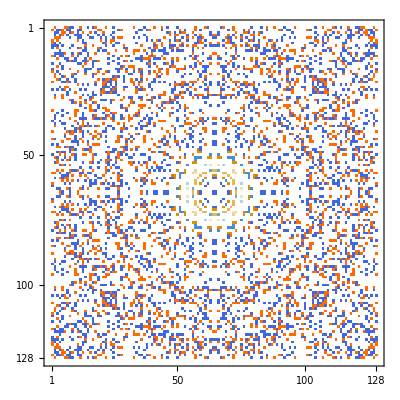

1.11022×10^-16

```mathematica
s0=FSkyrmion[10,1,π/2];
(* Import the result from Julia *)
s0julia = Transpose[Import[dir<>"initial-spin-field.h5","Data"][[1]],{3,2,1}];
MatrixPlot[s0[[3]]-s0julia[[3]]]
Max[Abs[s0[[3]]-s0julia[[3]]]]
```

## 2. Energy of spin field ✓

```mathematica
Energy[s0,H,ED]
```

-210.444

```mathematica
Import[dir<>"energy.h5","Data"] [[1]](*import saved julia value*)
```

-210.444

## 3. Convolution ✓

```mathematica
conv = ListConvolve[s0[[1]],VDyy];

convJulia = Transpose[Import[dir<>"convolution-result.h5","Data"][[1]]];
Print["Max difference between julia and Mathematica = ",Max[conv-convJulia]];
Row[{MatrixPlot[convJulia,PlotLegends->Automatic,PlotLabel->"Julia Result"],MatrixPlot[conv,PlotLegends->Automatic,PlotLabel->"Mathematica Result"]}]
```

Max difference between julia and Mathematica = 2.52195

-Graphics--Graphics-

## 4. VD Matrices

```mathematica
vdJulia = Import[dir<>"vddxx.h5","Data"][[1]];

If[pbc≠1.0,Row[{MatrixPlot[vdJulia[[1;;2Nx-1,1;;2Ny-1]]-VDxx,PlotLegends->Automatic, PlotLabel->"Difference"],
MatrixPlot[vdJulia,PlotLegends->Automatic],

MatrixPlot[VDxx,PlotLegends->Automatic]}],

Print["Cannot compare to Mathematica when PBC is true because the matrices are not the same size. "];
Row[{MatrixPlot[vdJulia,PlotLegends->Automatic],
MatrixPlot[VDxx,PlotLegends->Automatic]}]

]
```

Cannot compare to Mathematica when PBC is true because the matrices are not the same size.

-Graphics--Graphics-

## 5. DDI Field (FHD function)

```mathematica
juliaFHD =Transpose[Import[dir<>"fhdResult.h5","Data"][[1]]];
mmFHD = FHD[s0];
chooseZ=2;

Print["Maximum difference between the two = ", Max[juliaFHD[[All,All,chooseZ]]-mmFHD[[chooseZ]]]];
Row[{MatrixPlot[juliaFHD[[All,All,chooseZ]],PlotLegends->Automatic,PlotLabel->"Julia Result"],MatrixPlot[mmFHD[[chooseZ]],PlotLegends->Automatic,PlotLabel->"Mathematica Result"],MatrixPlot[mmFHD[[chooseZ]]-juliaFHD[[All,All,chooseZ]],PlotLegends->Automatic,PlotLabel->"Difference"]}]
```

Maximum difference between the two = 8.43769×10^-15

-Graphics--Graphics--Graphics-

Note that in julia I added an extra row and column of zeros to speed up computation

```mathematica
Print["Dimensions VDzz julia: ",Transpose[Import[dir<>"vddzz.h5","Data"][[1]]]//Dimensions]
Print["Dimensions VDzz MM: ", Dimensions[VDzz]]
```

Dimensions VDzz julia: {200,200}

Dimensions VDzz MM: {199,199}

## 6. Effective Field ✓

```mathematica
heff=HEff[s0,H,ED];

effFieldJulia = Transpose[Import[dir<>"effectiveField.h5","Data"][[1]],{3,2,1}];

Print["Maximum difference between results = ", Max[Abs[effFieldJulia[[1]]-heff[[1]]]]];

chooseZ=3;
Row[{MatrixPlot[effFieldJulia[[chooseZ]], PlotLabel->"Julia Result", PlotLegends->Automatic],
MatrixPlot[heff[[chooseZ]],PlotLabel->"Mathematica Result", PlotLegends->Automatic],MatrixPlot[effFieldJulia[[chooseZ]]-heff[[chooseZ]],PlotLegends->Automatic]}]
```

Maximum difference between results = 9.86017×10^-15

-Graphics--Graphics--Graphics-

## 7. After 10 RK steps, h = 0.2 ✓

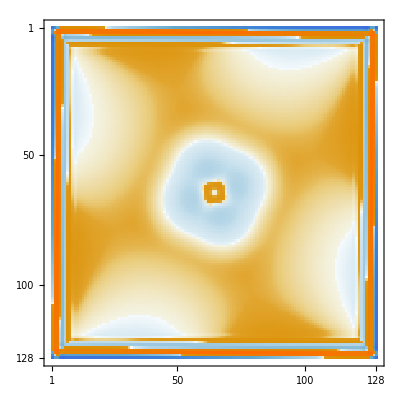
-Graphics--Graphics--Graphics-0.0329539

```mathematica
s0=FSkyrmion[10,1,π/2];
finalRK = Last@RK[s0,0.,1.0,10.,1.,{H,ED}];
juliaRK = Transpose[Import[dir<>"afterRk.h5","Data"][[1]],{3,2,1}];

Row[{MatrixPlot[juliaRK[[3]], PlotLabel->"Julia Result", PlotLegends->Automatic],
MatrixPlot[finalRK[[3]],PlotLabel->"Mathematica Result", PlotLegends->Automatic],
MatrixPlot[finalRK[[3]]-juliaRK[[3]]],
Max[Abs[finalRK[[3]]-juliaRK[[3]]]]
}]
```

# The rest of these have not been updated for DDI pbc

### After single noise rotation - hard to tell

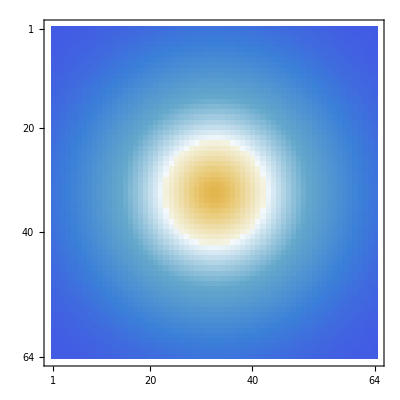

0.99005

-Graphics-

0.99005

```mathematica
mmNoise =NoiseRotation[s0,Sqrt[2damping T tFree]];
juliaNoise= Transpose[Import[dir<>"rotateSpins.h5","Data"][[1]],{3,2,1}];
MatrixPlot[mmNoise[[3]]]
Max[mmNoise[[3]]]
MatrixPlot[juliaNoise[[3]]]
Max[juliaNoise[[3]]]
```

### After single pulse noise

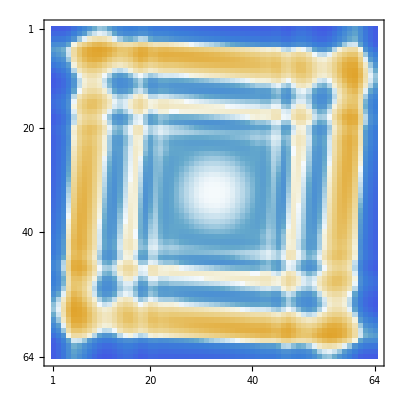

0.159825

```mathematica
mmPulse = Last@RK[s0,0.,5.0,25.,1.,{H,ED}];
mmPulse =NoiseRotation[mmPulse,Sqrt[2damping T tFree]];
mmPulse = Last@RK[mmPulse,0.,5.0,25.,1.,{H,ED}];
mmPulse=NormalizeSpins[mmPulse];

juliaPulse= Transpose[Import[dir<>"afterPulse.h5","Data"][[1]],{3,2,1}];
(*MatrixPlot[mmPulse[[3]]]*)
MatrixPlot[juliaPulse[[3]]-mmPulse[[3]]]
Max[Abs[juliaPulse[[3]]-mmPulse[[3]]]]
```